### The formulas, derivations and expressions, 1D

```mathematica
nEuler1D[ρm_,ξb_,dξ_]=-(2 dξ ⅇ^(-(2 (1+ρm))/ξb) (-2 ξb Hypergeometric0F1Regularized[1,(4 ρm)/ξb^2]+(ξb+4 ρm) Hypergeometric0F1Regularized[2,(4 ρm)/ξb^2]))/(√(2π) ξb^3 √(dξ ρm))
nEuler1DG[ρm_,ξb_,dξ_]=-Sqrt[dξ](ρm-1)Exp[-(ρm-1)^2/2/ξb]/(2 Pi ξb^(3/2))
```

-(dξ ⅇ^(-(2 (1+ρm))/ξb) √(2/π) (-2 ξb Hypergeometric0F1Regularized[1,(4 ρm)/ξb^2]+(ξb+4 ρm) Hypergeometric0F1Regularized[2,(4 ρm)/ξb^2]))/(ξb^3 √(dξ ρm))

-(√dξ ⅇ^(-(-1+ρm)^2/(2 ξb)) (-1+ρm))/(2 π ξb^(3/2))

```mathematica
(* construction of the function to be intergarted over λΔ for the computations of the extrema number densities *)
TL0[ρ_,φ0_,c0_,λc_]=c0 Exp[φ0-λc ρ] Hypergeometric0F1Regularized[2,c0 ρ];
TL1[ρ_,φ0_,c0_,λc_]=φ0 TL0[ρ,φ0,c0,λc]+c0 D[TL0[ρ,φ0,c0,λc],c0]//FullSimplify;
fc[λΔ_,dξ_]=(1+dξ λΔ/2)^2;
ϕextrem[ρ_,λΔ_,ξb_,dξ_,vξ_]=(√(1-dξ λΔ))/(√(2  π dξ ρ))TL0[ρ,-2/ξb,(2/ξb)^2 fc[λΔ,dξ],2/ξb fc[λΔ,dξ]-vξ λΔ^2/2]//FullSimplify
bϕextrem[ρ_,λΔ_,ξb_,dξ_,vξ_]=(√(1-dξ λΔ))/(√(2 π dξ ρ))TL1[ρ,-2/ξb,(2/ξb)^2 fc[λΔ,dξ],2/ξb fc[λΔ,dξ]-vξ λΔ^2/2]//FullSimplify
```

(ⅇ^(-(4+((2+dξ λΔ)^2-vξ λΔ^2 ξb) ρ)/(2 ξb)) √(1-dξ λΔ) (2+dξ λΔ)^2 Hypergeometric0F1Regularized[2,((2+dξ λΔ)^2 ρ)/ξb^2])/(√(2 π) ξb^2 √(dξ ρ))

1/(√(2 π) ξb^3 √(dξ ρ))ⅇ^(-(4+((2+dξ λΔ)^2-vξ λΔ^2 ξb) ρ)/(2 ξb)) √(1-dξ λΔ) (2+dξ λΔ)^2 (ξb Hypergeometric0F1Regularized[1,((2+dξ λΔ)^2 ρ)/ξb^2]-2 Hypergeometric0F1Regularized[2,((2+dξ λΔ)^2 ρ)/ξb^2])

```mathematica
nϕEuler1D[ρ_,ξb_,dξ_]=((D[ϕextrem[ρ,λΔ,ξb,dξ,vξ],λΔ])/.λΔ->0)//FullSimplify;
nϕEuler1D[ρ,ξb,dξ]-nEuler1D[ρ,ξb,dξ]//FullSimplify
```

0

```mathematica
bnEuler1D[ρ_,ξb_,dξ_]=((D[bϕextrem[ρ,λΔ,ξb,dξ,vξ],λΔ])/.λΔ->0)//FullSimplify
```

(dξ ⅇ^(-(2 (1+ρ))/ξb) √(2/π) (ξb (ξb-4 (1+ρ)) Hypergeometric0F1[1,(4 ρ)/ξb^2]+2 (ξb+8 ρ) Hypergeometric0F1[2,(4 ρ)/ξb^2]))/(ξb^4 √(dξ ρ))

```mathematica
nEuler1DG[1.04,.02,dξ]
nEuler1D[1.04,.02,dξ]
```

-2.16254 √dξ

-2.33321 √dξ

```mathematica
Clear[nmin1D,bnmin1D]
nmin1D[ρ_,ξb_,dξ_,vξ_]:=nmin1D[ρ,ξb,dξ,vξ]=NIntegrate[ϕextrem[ρ,I λΔ+1,ξb,dξ,vξ]/((I λΔ+1)^2)/(2 Pi),{λΔ,-Infinity,Infinity}]
bnmin1D[ρ_,ξb_,dξ_,vξ_]:=bnmin1D[ρ,ξb,dξ,vξ]:=NIntegrate[bϕextrem[ρ,I λΔ+1,ξb,dξ,vξ]/((I λΔ+1)^2)/(2 Pi),{λΔ,-Infinity,Infinity}]
```

```mathematica
Clear[nmax1D,bnmax1D]
nmax1D[ρ_,ξb_,dξ_,vξ_]:=nmax1D[ρ,ξb,dξ,vξ]=NIntegrate[ϕextrem[ρ,I λΔ-1,ξb,dξ,vξ]/((I λΔ-1)^2)/(2 Pi),{λΔ,-Infinity,Infinity}]
bnmax1D[ρ_,ξb_,dξ_,vξ_]:=bnmax1D[ρ,ξb,dξ,vξ]=NIntegrate[bϕextrem[ρ,I λΔ-1,ξb,dξ,vξ]/((I λΔ-1)^2)/(2 Pi),{λΔ,-Infinity,Infinity}]
```

```mathematica
listρ=Table[10^li,{li,-.8,.8,.05}];
```

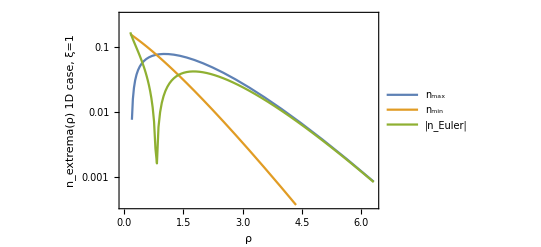

```mathematica
{Table[{ρ,nmax1D[ρ,1,.45,1.]//Re},{ρ,listρ}],Table[{ρ, nmin1D[ρ,1,.45,1.]//Re},{ρ,listρ}],Table[{ρ,nEuler1D[ρ,1,.45]//Re//Abs},{ρ,Table[10^li,{li,-0.8,.8,.02}]}]}//ListLogPlot[#,InterpolationOrder->1,Frame->True,Joined->True,
FrameLabel->{"ρ","n_extrema(ρ) 1D case, ξ̄=1"},PlotLegends->{"n_max","n_min","|n_Euler|"},PlotRange->{-.007,.3}]&
```

```mathematica
listρa=Table[10^li,{li,-.2,.8,.05}];
listρi=Table[10^li,{li,-.2,.8,.05}];
listρe=Table[10^li,{li,.1,.8,.05}];
```

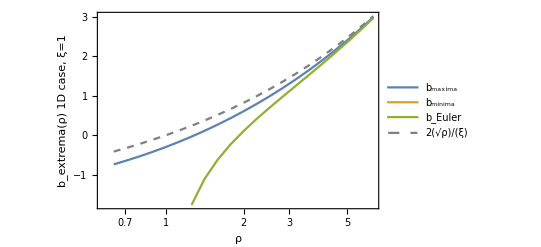

```mathematica
{Table[{ρ,bnmax1D[ρ,1,.45,1.]/nmax1D[ρ,1,.45,1.]//Re},{ρ,listρa}],Table[{ρ,( bnmin1D[ρ,1,.45,1.]/nmin1D[ρ,1,.45,1.])//Re},{ρ,listρi}],Table[{ρ,bnEuler1D[ρ,1,.45]/nEuler1D[ρ,1,.45]//Re},{ρ,listρe}],Table[{ρ,2 (Sqrt[ρ]-1)},{ρ,listρa}]}//ListLogLinearPlot[#,InterpolationOrder->1,Frame->True,Joined->True,PlotStyle->{Medium,Medium,Medium,{Dashed,Gray}},
FrameLabel->{"ρ","b_extrema(ρ) 1D case, ξ̄=1"},PlotLegends->{"b_maxima","b_minima","b_Euler","2(√ρ)/(ξ̄)"}]&
(*Export[NotebookDirectory[]<>"Bias_Extrema_2D_xb1.pdf",%]*)
```

### The formulas, 2D

```mathematica
(* Assumptions->{dξ>0,ξb>0, 8 vξ>dξ^2/ξb} *)
ac[λΔ_,λγ_,ξb_,dξ_,vξ_]=(2/ξb)^2((1+dξ λΔ/2)^2 );
λc[λΔ_,λγ_,ξb_,dξ_,vξ_]=2/ξb((1+dξ λΔ/2)^2-(1/12)vξ ξb(λγ^2+2λΔ^2));
ϕextrem2D[ρ_,λΔ_,λγ_,ξb_,dξ_,vξ_]=TL0[ρ,-2/ξb,ac[λΔ,λγ,ξb,dξ,vξ],λc[λΔ,λγ,ξb,dξ,vξ]](Pi √(4-4 dξ λΔ+dξ^2 (-λγ^2+λΔ^2)))/(dξ ρ (2 Pi)^2)
bϕextrem2D[ρ_,λΔ_,λγ_,ξb_,dξ_,vξ_]=TL1[ρ,-2/ξb,ac[λΔ,λγ,ξb,dξ,vξ],λc[λΔ,λγ,ξb,dξ,vξ]](Pi √(4-4 dξ λΔ+dξ^2 (-λγ^2+λΔ^2)))/(dξ ρ (2 Pi)^2)//FullSimplify
```

(ⅇ^(-2/ξb-(2 ((1+(dξ λΔ)/2)^2-1/12 vξ (λγ^2+2 λΔ^2) ξb) ρ)/ξb) (1+(dξ λΔ)/2)^2 √(4-4 dξ λΔ+dξ^2 (-λγ^2+λΔ^2)) Hypergeometric0F1Regularized[2,(4 (1+(dξ λΔ)/2)^2 ρ)/ξb^2])/(dξ π ξb^2 ρ)

1/(4 dξ π ξb^3 ρ)ⅇ^((-12-3 (2+dξ λΔ)^2 ρ+vξ (λγ^2+2 λΔ^2) ξb ρ)/(6 ξb)) (2+dξ λΔ)^2 √(-((2+dξ (λγ-λΔ)) (-2+dξ (λγ+λΔ)))) (ξb Hypergeometric0F1Regularized[1,((2+dξ λΔ)^2 ρ)/ξb^2]-2 Hypergeometric0F1Regularized[2,((2+dξ λΔ)^2 ρ)/ξb^2])

```mathematica
1/ρ ⅇ^(- aa ρ) Hypergeometric0F1Regularized[2,bb ρ]//FullSimplify
```

(ⅇ^(-aa ρ) Hypergeometric0F1Regularized[2,bb ρ])/ρ

```mathematica
Integrate[(ⅇ^(-aa ρ) Hypergeometric0F1Regularized[2,bb ρ])/ρ,{ρ,ρs,Infinity},Assumptions->{aa>0,bb>0}]
```

Integrate[(ⅇ^(-aa ρ) Hypergeometric0F1Regularized[2,bb ρ])/ρ,{ρ,ρs,∞},Assumptions→{aa>0,bb>0}]

```mathematica
nEuler2D[ρ_,ξb_,dξ_]=((D[ϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λΔ,2}]-1/λγ D[ϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λγ,1}]-D[ϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λγ,2}]//Simplify)/.{λΔ->0,λγ->0})//FullSimplify
```

(2 dξ ⅇ^(-(2 (1+ρ))/ξb) (ξb (4-3 ξb+4 ρ) Hypergeometric0F1Regularized[2,(4 ρ)/ξb^2]-2 (ξb+8 ρ) Hypergeometric0F1Regularized[3,(4 ρ)/ξb^2]))/(π ξb^5)

```mathematica
nEuler2DG[ρm_,ξb_,dξ_]=-(dξ ⅇ^(-(-1+ρm)^2/(2 ξb)) (ξb-(-1+ρm)^2))/(2 √2 π^(3/2) ξb^(5/2));
```

```mathematica
bnEuler2D[ρ_,ξb_,dξ_]=((D[bϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λΔ,2}]-1/λγ D[bϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λγ,1}]-D[bϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λγ,2}]//Simplify)/.{λΔ->0,λγ->0})//FullSimplify
```

(2 dξ ⅇ^(-(2 (1+ρ))/ξb) (ξb (ξb-3 ξb ρ+4 ρ (3+ρ)) Hypergeometric0F1Regularized[1,(4 ρ)/ξb^2]-(ξb^2+8 ρ (1+3 ρ)) Hypergeometric0F1Regularized[2,(4 ρ)/ξb^2]))/(π ξb^5 ρ)

```mathematica
Clear[nmax2D,nmin2D]
nmax2D[ρ_,ξb_,dξ_,vξ_]:=nmax2D[ρ,ξb,dξ,vξ]=NIntegrate[ϕextrem2D[ρ,I λκ-1,I λγ,ξb,dξ,vξ](12 π λγ)/((λγ^2+(I λκ-1)^2)^(5/2))/(2 Pi)^2,{λκ,-∞,∞},{λγ,0,∞}]
nmin2D[ρ_,ξb_,dξ_,vξ_]:=nmin2D[ρ,ξb,dξ,vξ]=NIntegrate[ϕextrem2D[ρ,I λκ+1,I λγ,ξb,dξ,vξ](12 π λγ)/((λγ^2+(I λκ+1)^2)^(5/2))/(2 Pi)^2,{λκ,-∞,∞},{λγ,0,∞}]
```

```mathematica
nsaddle[ρ_,ξb_,dξ_,vξ_]:=nmax2D[ρ,ξb,dξ,vξ]+nmin2D[ρ,ξb,dξ,vξ]-nEuler2D[ρ,ξb,dξ]
```

```mathematica
Clear[bnmax2D,bnmin2D]
bnmax2D[ρ_,ξb_,dξ_,vξ_]:=bnmax2D[ρ,ξb,dξ,vξ]=NIntegrate[bϕextrem2D[ρ,I λκ-1,I λγ,ξb,dξ,vξ](12 π λγ)/((λγ^2+(I λκ-1)^2)^(5/2))/(2 Pi)^2,{λκ,-∞,∞},{λγ,0,∞}]
bnmin2D[ρ_,ξb_,dξ_,vξ_]:=bnmin2D[ρ,ξb,dξ,vξ]=NIntegrate[bϕextrem2D[ρ,I λκ+1,I λγ,ξb,dξ,vξ](12 π λγ)/((λγ^2+(I λκ+1)^2)^(5/2))/(2 Pi)^2,{λκ,-∞,∞},{λγ,0,∞}]
```

```mathematica
bnsaddle[ρ_,ξb_,dξ_,vξ_]:=bnmax2D[ρ,ξb,dξ,vξ]+bnmin2D[ρ,ξb,dξ,vξ]-bnEuler2D[ρ,ξb,dξ]
```

```mathematica
listρ=Table[10^li,{li,-.8,.8,.05}];
```

```mathematica
ρ
listρ
```

0.501187

{0.158489,0.177828,0.199526,0.223872,0.251189,0.281838,0.316228,0.354813,0.398107,0.446684,0.501187,0.562341,0.630957,0.707946,0.794328,0.891251,1.,1.12202,1.25893,1.41254,1.58489,1.77828,1.99526,2.23872,2.51189,2.81838,3.16228,3.54813,3.98107,4.46684,5.01187,5.62341,6.30957}

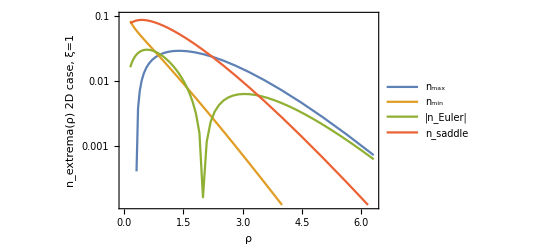

```mathematica
{Table[{ρ,nmax2D[ρ,1,.45,1.5]//Re},{ρ,listρ}],Table[{ρ, nmin2D[ρ,1,.45,1.5]//Re},{ρ,listρ}],Table[{ρ,nEuler2D[ρ,1,.45]//Re//Abs},{ρ,Table[10^li,{li,-0.8,.8,.02}]}],Table[{ρ,nsaddle[ρ,1,.45,1.5]//Re},{ρ,listρ}]}//ListLogPlot[#,InterpolationOrder->1,Frame->True,Joined->True,
FrameLabel->{"ρ","n_extrema(ρ) 2D case, ξ̄=1"},PlotLegends->{"n_max","n_min","|n_Euler|","n_saddle"},PlotRange->{-.005,.1}]&
```

```mathematica
listρa=Table[10^li,{li,.2,1.2,.05}];
listρi=Table[10^li,{li,-.4,1.2,.05}];
listρe=Table[10^li,{li,.45,1.2,.05}];
listρs=Table[10^li,{li,-.1,1.2,.05}];
```

```mathematica
ρ
listρs
```

3.98107

{0.794328,0.891251,1.,1.12202,1.25893,1.41254,1.58489,1.77828,1.99526,2.23872,2.51189,2.81838,3.16228,3.54813,3.98107,4.46684,5.01187,5.62341,6.30957,7.07946,7.94328,8.91251,10.,11.2202,12.5893,14.1254,15.8489}

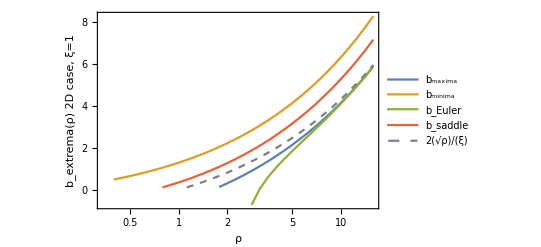

```mathematica
{Select[Table[{ρ,bnmax2D[ρ,1,.45,1.5]/nmax2D[ρ,1,.45,1.5]//Re},{ρ,listρa}],#[[2]]>0&],Table[{ρ, bnmin2D[ρ,1,.45,1.5]/nmin2D[ρ,1,.45,1.5]//Re},{ρ,listρi}],Table[{ρ,bnEuler2D[ρ,1,.45]/nEuler2D[ρ,1,.45]//Re},{ρ,listρe}],Table[{ρ,bnsaddle[ρ,1,.45,1.5]/nsaddle[ρ,1,.45,1.5]//Re},{ρ,listρs}]//Select[#,#[[2]]>0&]&,Table[{ρ,2 (Sqrt[ρ]-1)},{ρ,listρs}]//Select[#,#[[2]]>0&]&}//ListLogLinearPlot[#,InterpolationOrder->1,Frame->True,Joined->True,PlotStyle->{Medium,Medium,Medium,Medium,{Dashed,Gray},{Dotted,Gray}},
FrameLabel->{"ρ","b_extrema(ρ) 2D case, ξ̄=1"},PlotLegends->{"b_maxima","b_minima","b_Euler","b_saddle","2(√ρ)/(ξ̄)"}]&
```

```mathematica
cnEuler2D[ρc_,ξb_,dξ_]:=NIntegrate[nEuler2D[ρ,ξb,dξ],{ρ,ρc,20}]
cbnEuler2D[ρc_,ξb_,dξ_]:=NIntegrate[bnEuler2D[ρ,ξb,dξ],{ρ,ρc,20}]
```

```mathematica
ϕextrem2Da[ρ_,λκ_,ξb_,dξ_,vξ_]=(1+(dξ λκ)/2)^2 ⅇ^(-2/ξb-(2 ((1+(dξ λκ)/2)^2-1/12 vξ (2 λκ^2) ξb) ρ)/ξb)Hypergeometric0F1Regularized[2,(4 (1+(dξ λκ)/2)^2 ρ)/ξb^2]/(dξ π ξb^2 ρ)
ϕextrem2Db[ρ_,λκ_,λγ_,ξb_,dξ_,vξ_]=ⅇ^(-(2 (-1/12 vξ (λγ^2) ξb) ρ)/ξb)
ϕextrem2Dc[ρ_,λκ_,λγ_,ξb_,dξ_,vξ_]=√(4-4 dξ λκ+dξ^2 (-λγ^2+λκ^2))
```

(ⅇ^(-2/ξb-(2 ((1+(dξ λκ)/2)^2-1/6 vξ λκ^2 ξb) ρ)/ξb) (1+(dξ λκ)/2)^2 Hypergeometric0F1Regularized[2,(4 (1+(dξ λκ)/2)^2 ρ)/ξb^2])/(dξ π ξb^2 ρ)

ⅇ^(1/6 vξ λγ^2 ρ)

√(4-4 dξ λκ+dξ^2 (-λγ^2+λκ^2))

```mathematica
NIntegrate[ϕextrem2D[ρ,I λκ+1,I λγ,ξb,dξ,vξ](12 π λγ)/((λγ^2+(I λκ+1)^2)^(5/2))/(2 Pi)^2,{λκ,-∞,∞},{λγ,0,∞}]
```

NIntegrate[(ϕextrem2D[ρ,ⅈ λκ+1,ⅈ λγ,ξb,dξ,vξ] (12 π λγ))/((λγ^2+(ⅈ λκ+1)^2)^(5/2) (2 π)^2),{λκ,-∞,∞},{λγ,0,∞}]

```mathematica
ϕextrem2Dd[ρ_,λκ_,p_,ξb_,dξ_,vξ_]=(ϕextrem2Db[ρ,λκ,I λγ,ξb,dξ,vξ] (12 π λγ)/((λγ^2+λκ^2)^(5/2))/(2 Pi)^2)//Simplify//Integrate[# (λγ)^(2 p),{λγ,0,Infinity},Assumptions->{Re[λκ]≠0&&(Re[λκ^2]≥0||λκ^2∉Reals)&&Re[vξ ρ]>0,p In Integers,p>0}]&
```

(√(λκ^2) (6^(-1/2+p) √(1/λκ^2) (vξ ρ)^(3/2-p) Gamma[-3/2+p] Hypergeometric1F1[5/2,5/2-p,1/6 vξ λκ^2 ρ]+(8 (1/λκ^2)^-p Gamma[3/2-p] Gamma[1+p] Hypergeometric1F1[1+p,-1/2+p,1/6 vξ λκ^2 ρ])/(√π λκ^4)))/(4 π)

```mathematica
Clear[ϕextrem2Dcp]
ϕextrem2Dcp[ρ_,λκ_,p_,ξb_,dξ_,vξ_]:=Series[ϕextrem2Dc[ρ,λκ,λγ,ξb,dξ,vξ],{λγ,0,2 p}]//Coefficient[#,λγ,2p]&
```

```mathematica
ϕextrem2Dr[ρ_,λκ_,ξb_,dξ_,vξ_]=Sum[ (-1)^p ϕextrem2Da[ρ,λκ,ξb,dξ,vξ]ϕextrem2Dd[ρ,λκ,p,ξb,dξ,vξ]ϕextrem2Dcp[ρ ,λκ,p,ξb,dξ,vξ],{p,0,5,1}]//Simplify
```

(ⅇ^(-(2 (1+((1+(dξ λκ)/2)^2-1/6 vξ λκ^2 ξb) ρ))/ξb) √(λκ^2) (2+dξ λκ)^2 √(vξ ρ) (vξ ρ (262144 vξ^3 ρ^3 (ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) vξ^2 √(1/λκ^2) λκ^4 ρ^2-6 √(vξ ρ) (-3+vξ λκ^2 ρ))-1310720 dξ vξ^3 λκ ρ^3 (ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) vξ^2 √(1/λκ^2) λκ^4 ρ^2-6 √(vξ ρ) (-3+vξ λκ^2 ρ))+(131072 dξ^3 vξ^3 λκ^3 ρ^3 (6 √(1/λκ^2) √(vξ ρ) (-96+29 vξ λκ^2 ρ)-ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) vξ ρ (-9+29 vξ λκ^2 ρ)))/(√(1/λκ^2))-32768 dξ^2 vξ^3 λκ^2 ρ^3 (6 √(vξ ρ) (-276+89 vξ λκ^2 ρ)-(ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) vξ ρ (-9+89 vξ λκ^2 ρ))/(√(1/λκ^2)))-2048 dξ^4 vξ^3 λκ^4 ρ^3 (6 √(vξ ρ) (-5727+1567 vξ λκ^2 ρ)+ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) √(1/λκ^2) (27+1026 vξ λκ^2 ρ-1567 vξ^2 λκ^4 ρ^2))+(2048 dξ^5 vξ^3 λκ^3 ρ^3 ((6 √(vξ ρ) (-3741+893 vξ λκ^2 ρ))/(√(1/λκ^2))+ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) (81+1062 vξ λκ^2 ρ-893 vξ^2 λκ^4 ρ^2)))/(√(1/λκ^2))-768 dξ^6 vξ^2 λκ^4 ρ^2 (6 √(vξ ρ) (-9-4638 vξ λκ^2 ρ+923 vξ^2 λκ^4 ρ^2)+ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) √(1/λκ^2) (-27+297 vξ λκ^2 ρ+1869 vξ^2 λκ^4 ρ^2-923 vξ^3 λκ^6 ρ^3))+(1536 dξ^7 vξ^2 λκ^3 ρ^2 ((6 √(vξ ρ) (-9-762 vξ λκ^2 ρ+119 vξ^2 λκ^4 ρ^2))/(√(1/λκ^2))+ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) (-27+117 vξ λκ^2 ρ+405 vξ^2 λκ^4 ρ^2-119 vξ^3 λκ^6 ρ^3)))/(√(1/λκ^2))-24 dξ^8 vξ λκ^4 ρ (6 √(vξ ρ) (405-567 vξ λκ^2 ρ-10983 vξ^2 λκ^4 ρ^2+1225 vξ^3 λκ^6 ρ^3)+ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) √(1/λκ^2) (1215-1836 vξ λκ^2 ρ+3726 vξ^2 λκ^4 ρ^2+7308 vξ^3 λκ^6 ρ^3-1225 vξ^4 λκ^8 ρ^4))+1/(√(1/λκ^2))72 dξ^9 vξ λκ^3 ρ ((6 √(vξ ρ) (135-93 vξ λκ^2 ρ-525 vξ^2 λκ^4 ρ^2+35 vξ^3 λκ^6 ρ^3))/(√(1/λκ^2))+ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) (405-324 vξ λκ^2 ρ+378 vξ^2 λκ^4 ρ^2+420 vξ^3 λκ^6 ρ^3-35 vξ^4 λκ^8 ρ^4))-9 dξ^10 λκ^4 (6 √(vξ ρ) (-2835+900 vξ λκ^2 ρ-264 vξ^2 λκ^4 ρ^2-336 vξ^3 λκ^6 ρ^3+7 vξ^4 λκ^8 ρ^4)+ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) √(1/λκ^2) (-8505+3645 vξ λκ^2 ρ-1134 vξ^2 λκ^4 ρ^2+630 vξ^3 λκ^6 ρ^3+315 vξ^4 λκ^8 ρ^4-7 vξ^5 λκ^10 ρ^5)))+ⅇ^(1/6 vξ λκ^2 ρ) √(6 π) λκ^2 √(vξ ρ) √(vξ λκ^2 ρ) (-262144 vξ^5 ρ^5+1310720 dξ vξ^5 λκ ρ^5+131072 dξ^3 vξ^4 λκ ρ^4 (-9+29 vξ λκ^2 ρ)-32768 dξ^2 vξ^4 ρ^4 (-9+89 vξ λκ^2 ρ)+2048 dξ^5 vξ^3 λκ ρ^3 (-81-1062 vξ λκ^2 ρ+893 vξ^2 λκ^4 ρ^2)-2048 dξ^4 vξ^3 ρ^3 (-27-1026 vξ λκ^2 ρ+1567 vξ^2 λκ^4 ρ^2)+1536 dξ^7 vξ^2 λκ ρ^2 (27-117 vξ λκ^2 ρ-405 vξ^2 λκ^4 ρ^2+119 vξ^3 λκ^6 ρ^3)-768 dξ^6 vξ^2 ρ^2 (27-297 vξ λκ^2 ρ-1869 vξ^2 λκ^4 ρ^2+923 vξ^3 λκ^6 ρ^3)+72 dξ^9 vξ λκ ρ (-405+324 vξ λκ^2 ρ-378 vξ^2 λκ^4 ρ^2-420 vξ^3 λκ^6 ρ^3+35 vξ^4 λκ^8 ρ^4)-24 dξ^8 vξ ρ (-1215+1836 vξ λκ^2 ρ-3726 vξ^2 λκ^4 ρ^2-7308 vξ^3 λκ^6 ρ^3+1225 vξ^4 λκ^8 ρ^4)-9 dξ^10 (8505-3645 vξ λκ^2 ρ+1134 vξ^2 λκ^4 ρ^2-630 vξ^3 λκ^6 ρ^3-315 vξ^4 λκ^8 ρ^4+7 vξ^5 λκ^10 ρ^5)) Erf[(√(vξ λκ^2 ρ))/(√6)]) Hypergeometric0F1Regularized[2,((2+dξ λκ)^2 ρ)/ξb^2])/(18432 dξ π^2 vξ^5 λκ^4 (-2+dξ λκ)^8 √((-2+dξ λκ)^2) ξb^2 ρ^6)

```mathematica
Clear[nmin2Dr]
nmin2Dr[ρ_,ξb_,dξ_,vξ_]:= NIntegrate[ ϕextrem2Dr[ρ,I λκ+.5,ξb,dξ,vξ],{λκ,-30,30}]
```

```mathematica
nmin2D[.55,1.,.45,1.5]//Timing
nmin2Dr[1.55,1.,.45,1.5]//Timing
```

{18.1089,0.0407776-2.35922×10^-16 ⅈ}

{152.276,-6.69945×10^22+4.38908×10^22 ⅈ}

```mathematica
lρc
```

0.7

```mathematica
Clear[fmin2D,fmax2D,fbmin2D,fbmax2D]
fmin2D[ξb_,dξ_,vξ_]:=(tmin=Table[{lρc,10^lρc nmin2D[10^lρc,ξb,dξ,vξ]},{lρc,-1,1.2,.02}]//Interpolation;1/# tmin[Log[10,#]]&)
fmax2D[ξb_,dξ_,vξ_]:=(tmax=Table[{lρc,10^lρc nmax2D[10^lρc,ξb,dξ,vξ]},{lρc,-1,1.2,.02}]//Interpolation;1/# tmax[Log[10,#]]&)
fbmin2D[ξb_,dξ_,vξ_]:=(tbmin=Table[{lρc,10^lρc bnmin2D[10^lρc,ξb,dξ,vξ]},{lρc,-1,1.2,.02}]//Interpolation;1/# tbmin[Log[10,#]]&)
fbmax2D[ξb_,dξ_,vξ_]:=(tbmax=Table[{lρc,10^lρc bnmax2D[10^lρc,ξb,dξ,vξ]},{lρc,-1,1.2,.02}]//Interpolation;1/# tbmax[Log[10,#]]&)
```

```mathematica
lρc
```

lρc

0.583993

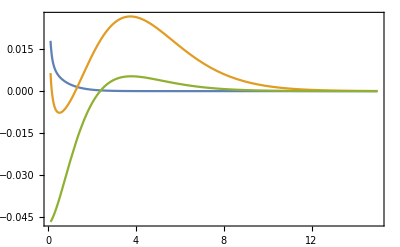

```mathematica
ξ2t=1.62;
ξ2t=1.634;
gCP={0.579995, 0.583815,0.597639, 0.598497, 0.575236, 0.583534, 0.58128, 0.588755, 0.584855, 0.584074, 0.590854, 0.593123, 0.587903, 0.579013, 0.583058, 0.571181, 0.587212, 0.57657,0.586477,0.574375, 0.570697, 0.576817, 0.576048,0.584713, 0.593254, 0.599971, 0.593544, 0.578663, 0.583419, 0.577855, 0.581349}//Mean
Plot[{r fmin2D[ξ2t,ξ2t gCP,ξ2t][r]//Re,r fmax2D[ξ2t,ξ2t gCP,ξ2t][r]//Re,nEuler2D[r,ξ2t,ξ2t gCP] },{r,.1,15},Frame->True,PlotRange->All]
```

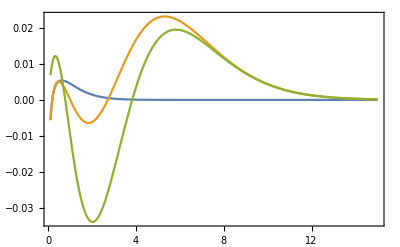

```mathematica
Plot[{r fbmin2D[ξ2t,ξ2t gCP,ξ2t ][r]//Re,r fbmax2D[ξ2t,ξ2t gCP,ξ2t][r]//Re,r bnEuler2D[r,ξ2t,ξ2t gCP] },{r,.1,15},Frame->True,PlotRange->All]
```

```mathematica
Clear[cmax2D,cmin2D,cbmax2D,cbmin2D,cEul2D,cbEul2D]
cmax2D[ξb_,dξ_,vξ_]:=cmax2D[ξb,dξ,vξ]=NIntegrate[fmax2D[ξb,dξ,vξ][x],{x,#,15.}]&
cmin2D[ξb_,dξ_,vξ_]:=cmin2D[ξb,dξ,vξ]=NIntegrate[fmin2D[ξb,dξ,vξ][x],{x,#,15.}]&
cbmax2D[ξb_,dξ_,vξ_]:=cbmax2D[ξb,dξ,vξ]=NIntegrate[fbmax2D[ξb,dξ,vξ][x],{x,#,15.}]&
cbmin2D[ξb_,dξ_,vξ_]:=cbmin2D[ξb,dξ,vξ]=NIntegrate[fbmin2D[ξb,dξ,vξ][x],{x,#,15.}]&
cEul2D[ξb_,dξ_,vξ_]:=cEul2D[ξb,dξ,vξ]=NIntegrate[nEuler2D[x,ξb,dξ],{x,#,15.}]&
cbEul2D[ξb_,dξ_,vξ_]:=cbEul2D[ξb,dξ,vξ]=NIntegrate[bnEuler2D[x,ξb,dξ],{x,#,15.}]&
```

```mathematica
cSaddle2D[ξb_,dξ_,vξ_]:=(cmax2D[ξb,dξ,vξ][#]+cmin2D[ξb,dξ,vξ][#]-cEul2D[ξb,dξ,vξ][#])&
cbSaddle2D[ξb_,dξ_,vξ_]:=(cbmax2D[ξb,dξ,vξ][#]+cbmin2D[ξb,dξ,vξ][#]-cbEul2D[ξb,dξ,vξ][#])&
```

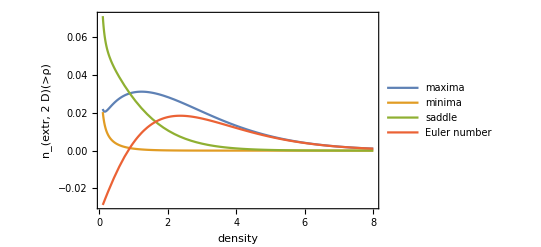

/Users/francisbernardeauipht/Dropbox/Peak Statistics/cumulative_densities.pdf

```mathematica
Plot[{cmax2D[ξ2t,ξ2t gCP,ξ2t][r]//Re,cmin2D[ξ2t,ξ2t gCP,ξ2t][r]//Re,cSaddle2D[ξ2t,ξ2t gCP,ξ2t][r]//Re,cEul2D[ξ2t,ξ2t gCP,ξ2t][r] },{r,.1,8},Frame->True,PlotRange->All,LabelStyle->{Bold,Medium},FrameLabel->{"density","n_(extr,  2  D)(>ρ)"},PlotLegends->{"maxima","minima","saddle","Euler number"}]
Export[NotebookDirectory[]<>"cumulative_densities.pdf",%]
```

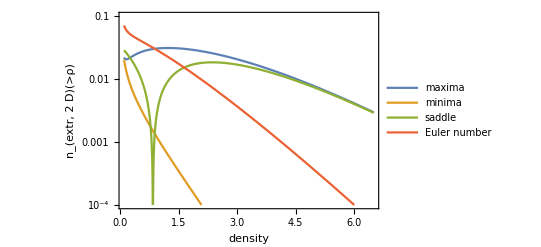

```mathematica
LogPlot[{cmax2D[ξ2t,ξ2t gCP,ξ2t][r]//Re,cmin2D[ξ2t,ξ2t gCP,ξ2t][r]//Re,cEul2D[ξ2t,ξ2t gCP,ξ2t][r]//Abs ,cSaddle2D[ξ2t,ξ2t gCP,ξ2t][r]//Re},{r,.1,6.5},Frame->True,LabelStyle->{Bold,Medium},FrameLabel->{"density","n_(extr,  2  D)(>ρ)"},PlotLegends->{"maxima","minima","saddle","Euler number"},PlotRange->{All,{.0001,.1}}]
```

```mathematica
(* <PastedGraphic-3.png>{-Graphics-}*)
```

```mathematica
Color1=RGBColor[94./255,129./255,182./255];
Color2=RGBColor[225./255,156./255,36./255];
Color3=RGBColor[143./255,176./255,50./255];
Color4=RGBColor[235./255,98./255,53./255];
Color5=RGBColor[135./255,120./255,179./255];
```

```mathematica
cEul2D[ξ2t,ξ2t gCP,ξ2t][.2]
```

-0.0241362

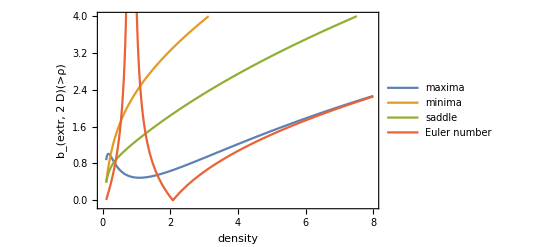

/Users/francisbernardeauipht/Dropbox/Peak Statistics/cumulative_bias.pdf

```mathematica
Show[Plot[{(cbmax2D[ξ2t,ξ2t gCP,ξ2t][r]/cmax2D[ξ2t,ξ2t gCP,ξ2t][r])//Re,(cbmin2D[ξ2t,ξ2t gCP,ξ2t][r]/cmin2D[ξ2t,ξ2t gCP,ξ2t][r])//Re,(cbSaddle2D[ξ2t,ξ2t gCP,ξ2t][r]/cSaddle2D[ξ2t,ξ2t gCP,ξ2t][r])//Re},{r,.1,8},Frame->True,LabelStyle->{Bold,Medium},FrameLabel->{"density","b_(extr,  2  D)(>ρ)"},PlotLegends->{"maxima","minima","saddle"},PlotRange->{-.1,4.}],Plot[{cbEul2D[ξ2t,ξ2t gCP,ξ2t][r]/cEul2D[ξ2t,ξ2t gCP,ξ2t][r]//Abs },{r,.1,8},Frame->True,PlotStyle->{Color4},LabelStyle->{Bold,Medium},FrameLabel->{"density","b_(extr,  2  D)(>ρ)"},PlotLegends->{"Euler number"}]]
Export[NotebookDirectory[]<>"cumulative_bias.pdf",%]
```

### The formulas, 3D

```mathematica
nEuler3D[ρm_,ξb_,dξ_]=-1/(2 Sqrt[2] π^(3/2) ξb^5 ρm^3)ⅇ^(-(2 (1+ρm))/ξb) (dξ ρm)^(3/2) (-ξb (3 ξb^2+16 ρm (1+3 ρm)) Hypergeometric0F1Regularized[1,(4 ρm)/ξb^2]+(3 ξb^3+16 ξb ρm+6 ξb^2 ρm+32 ρm^2 (3+ρm)) Hypergeometric0F1Regularized[2,(4 ρm)/ξb^2])
nEuler3DG[ρm_,ξb_,dξ_]=-(dξ^(3/2) ⅇ^(-(-1+ρm)^2/(2 ξb)) (-3 ξb+(-1+ρm)^2) (-1+ρm))/(4 π^2 ξb^(7/2))
```

-1/(2 √2 π^(3/2) ξb^5 ρm^3)ⅇ^(-(2 (1+ρm))/ξb) (dξ ρm)^(3/2) (-ξb (3 ξb^2+16 ρm (1+3 ρm)) Hypergeometric0F1Regularized[1,(4 ρm)/ξb^2]+(3 ξb^3+16 ξb ρm+6 ξb^2 ρm+32 ρm^2 (3+ρm)) Hypergeometric0F1Regularized[2,(4 ρm)/ξb^2])

-(dξ^(3/2) ⅇ^(-(-1+ρm)^2/(2 ξb)) (-3 ξb+(-1+ρm)^2) (-1+ρm))/(4 π^2 ξb^(7/2))

### Plots of Euler number densities as a function of cumulative probs.

```mathematica
PDFG[ρ_,ξb_]=Exp[-(ρ-1)^2/2/ξb]/Sqrt[2 Pi ξb];
PDFNL[ρ_, ξb_] = (4*Hypergeometric0F1Regularized[2, (4*ρ)/ξb^2])/
     (E^((2*(1 + ρ))/ξb)*ξb^2);
```

```mathematica
Clear[cnEuler1DG,cnEuler2DG,cnEuler3DG]
cPDFG[ρ_,ξb_]=Integrate[PDFG[ρm,ξb],{ρm,-Infinity,ρ},Assumptions->{ξb>0}];
cnEuler1DG[ρ_,ξb_,dξ_]=Integrate[nEuler1DG[ρm,ξb,dξ],{ρm,-Infinity,ρ},Assumptions->{ξb>0}]
cnEuler2DG[ρ_,ξb_,dξ_]=Integrate[nEuler2DG[ρm,ξb,dξ],{ρm,-Infinity,ρ},Assumptions->{ξb>0}]
cnEuler3DG[ρ_,ξb_,dξ_]=Integrate[nEuler3DG[ρm,ξb,dξ],{ρm,-Infinity,ρ},Assumptions->{ξb>0}]
```

(ⅇ^(-(-1+ρ)^2/(2 ξb)) √(dξ/ξb))/(2 π)

-(dξ ⅇ^(-(-1+ρ)^2/(2 ξb)) (-1+ρ))/(2 √2 π^(3/2) ξb^(3/2))

(dξ^(3/2) ⅇ^(-(-1+ρ)^2/(2 ξb)) (-ξb+(-1+ρ)^2))/(4 π^2 ξb^(5/2))

```mathematica
Clear[cPDFNL,cnEuler1D,cnEuler2D,cnEuler3D]
cPDFNL[ρ_,ξb_]:=cPDFNL[ρ,ξb]=NIntegrate[PDFNL[ρm, ξb],{ρm,0.,ρ}]+Exp[-2/ξb]
cnEuler1D[ρ_,ξb_,dξ_]:=cnEuler1D[ρ,ξb,dξ]=NIntegrate[nEuler1D[ρm,ξb,dξ],{ρm,0.,ρ}];
cnEuler2D[ρ_,ξb_,dξ_]:=cnEuler2D[ρ,ξb,dξ]=dξ Exp[-2/ξb]/ξb^2/( Pi)+NIntegrate[nEuler2D[ρm,ξb,dξ],{ρm,0.,ρ}];cnEuler3D[ρ_,ξb_,dξ_]:=cnEuler3D[ρ,ξb,dξ]=NIntegrate[nEuler3D[ρm,ξb,dξ],{ρm,0.,ρ}];
```

```mathematica
Color1=RGBColor[94./255,129./255,182./255];
Color2=RGBColor[225./255,156./255,36./255];
Color3=RGBColor[143./255,176./255,50./255];
Color4=RGBColor[235./255,98./255,53./255];
Color5=RGBColor[135./255,120./255,179./255];

LColor1=Color1//Lighter//Lighter//Lighter;
LColor2=Color2//Lighter//Lighter//Lighter;
LColor3=Color3//Lighter//Lighter//Lighter;
LColor4=Color4//Lighter//Lighter//Lighter;
```

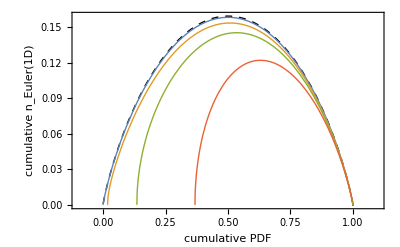

```mathematica
ParametricPlot[{{cPDFG[ρm+4,.1],cnEuler1DG[ρm+4,.1,.1]},{cPDFNL[ρm+4,.1], cnEuler1D[ρm+4,.1,.1]},{cPDFNL[ρm+4,.5],cnEuler1D[ρm+4,.5,.5]},{cPDFNL[ρm+4,1.],cnEuler1D[ρm+4,1.,1.]},{cPDFNL[ρm+4,2.],cnEuler1D[ρm+4,2.,2.]}},{ρm,-4,4},Frame->True,AspectRatio->1/GoldenRatio,PlotStyle->{{Thick,Dashed,Black},{Thick,Color1},{Thick,Color2},{Thick,Color3},{Thick,Color4},{Dashed,Color4}},LabelStyle->{Bold,Medium},FrameLabel->{"cumulative PDF","cumulative n_Euler(1D)"},PlotRange->{{-.1,1.1},Automatic}]
```

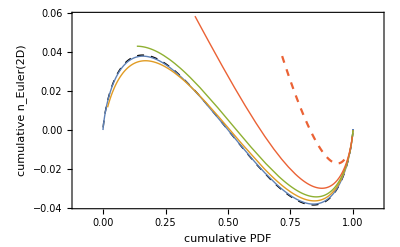

```mathematica
ParametricPlot[{{cPDFG[ρm+4,.1],cnEuler2DG[ρm+4,.1,.1]},{cPDFNL[ρm+4,.1],cnEuler2D[ρm+4,.1,.1]},{cPDFNL[ρm+4,.5],cnEuler2D[ρm+4,.5,.5]},{cPDFNL[ρm+4,1.],cnEuler2D[ρm+4,1.,1.]},{cPDFNL[ρm+4,2.],cnEuler2D[ρm+4,2.,2.]},{cPDFNL[ρm+4,6.],cnEuler2D[ρm+4,6.,6.]}},{ρm,-4,4},Frame->True,AspectRatio->1/GoldenRatio,PlotStyle->{{Thick,Dashed,Black},{Thick,Color1},{Thick,Color2},{Thick,Color3},{Thick,Color4},{Dashed,Color4}},LabelStyle->{Bold,Medium},FrameLabel->{"cumulative PDF","cumulative n_Euler(2D)"},PlotRange->{{-.1,1.1},All}]
```

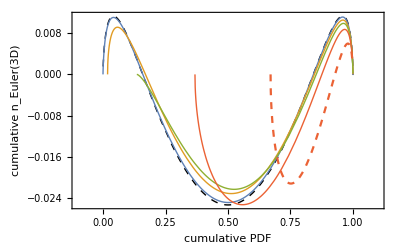

```mathematica
ParametricPlot[{{cPDFG[ρm+4,.1], cnEuler3DG[ρm+4,.1,.1]},{cPDFNL[ρm+4,.1],cnEuler3D[ρm+4,.1,.1]},{cPDFNL[ρm+4,.5],cnEuler3D[ρm+4,.5,.5]},{cPDFNL[ρm+4,1.],cnEuler3D[ρm+4,1.,1.]},{cPDFNL[ρm+4,2.],cnEuler3D[ρm+4,2.,2.]},{cPDFNL[2 ρm+8,5.],cnEuler3D[2 ρm+8,5.,5.]}},{ρm,-4,4},Frame->True,AspectRatio->1/GoldenRatio,PlotStyle->{{Thick,Dashed,Black},{Thick,Color1},{Thick,Color2},{Thick,Color3},{Thick,Color4},{Dashed,Color4}},LabelStyle->{Bold,Medium},FrameLabel->{"cumulative PDF","cumulative n_Euler(3D)"},PlotRange->{{-.1,1.1},All}]
```